```mathematica
Map[Length[KSetPartitions[#,2]]&,{Join[Range[1],Range[3,3]],Join[Range[2,2],Range[6,8]],Join[Range[4,4],Range[9,11]],Join[Range[5,5],Range[12,14]]}]//Total
```

22

```mathematica
{Join[Range[1],Range[3,3]],Join[Range[2,2],Range[6,8]],Join[Range[4,4],Range[9,11]],Join[Range[5,5],Range[12,14]]}
```

{{1,3},{2,6,7,8},{4,9,10,11},{5,12,13,14}}

```mathematica
SetsToSymbol2[{{1,3},{2,6,7,8},{4,9,10,11},{5,12,13,14}}]
```

v13x2678x49abx5cde

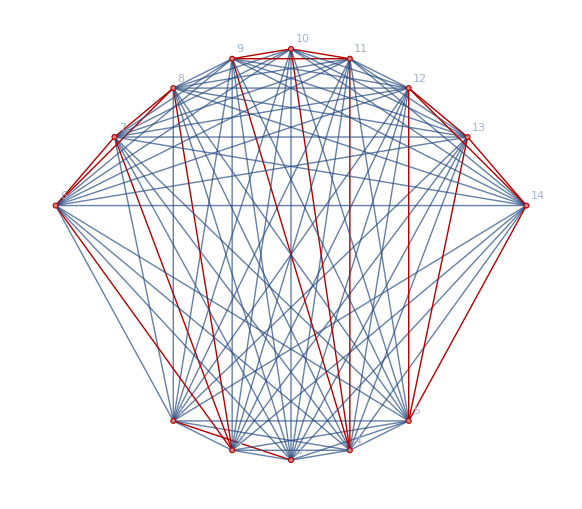

```mathematica
Framed[GraphFromSymbol[v13x2678x49abx5cde]]
```

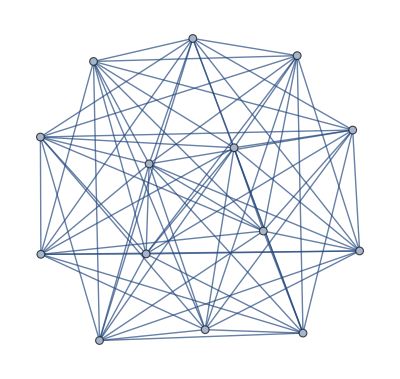

```mathematica
g=Graph[GraphFromSets[{Join[Range[1],Range[3,3]],Join[Range[2,2],Range[6,8]],Join[Range[4,4],Range[9,11]],Join[Range[5,5],Range[12,14]]}]]
```

```mathematica
ChromaticPolynomial[g,5]
```

```mathematica
2760/120
```

23